```mathematica
[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive
```

# Формулы

```mathematica
"Символы"paclet:tutorial/LettersAndLetterLikeForms
```

( = esc)

a → α
b → β
γ → γ
…
f → ϕ    j → φ
e → ϵ  ce → ε
w → ω  o → ω     om → ο

deg  → °

```mathematica
α β ϕ φ
```

```mathematica
"Набор формул"paclet:tutorial/KeyboardShortcutListing#1484044289
```

Ctrl+6 → □^□
Ctrl+2 → √□
…+Ctrl+5 → □^(1/□)
Ctrl+/→ □/□
Ctrl+Space → end subexpression
Alt+/→ (*comment*)

Alt+ ),],}→ (),[],{}
Ctrl+,→  | □ | □ | □
Ctrl+Enter → □
□
□
…→(□ | □ | □
□ | □ | □
□ | □ | □)

```mathematica
"TeX"paclet:tutorial/GeneratingAndImportingTeX
```

TeXForm[]
MaTeX[]
ToExpression[,TeXForm]

```mathematica
TeXForm[(x 4^(1/3)√(1+x^5))/5]
```

\frac{1}{5} 2^{2/3} x \sqrt{x^5+1}

Можно также использовать функцию Copy As для непосредственного перенесения формул в TeX

```mathematica
ToExpression["\\sqrt{1+x^2}",TeXForm]
```

√(1+x^2)

```mathematica
Needs["MaTeX`"]; (*!Требует отдельной установки*)
MaTeX[TeXForm[HoldForm[(x 4^(1/3)√(1+x^5))/5]]]
```

-Graphics-

```mathematica
["Установка MaTeX"](https://github.com/szhorvat/MaTeX)
```

запустить скрипт и следовать дальнейшим инструкциям для связи с pdflaTeX и GhostScript:

```mathematica
Needs["PacletManager`"];
pacletfile=URLDownload["https://github.com/szhorvat/MaTeX/releases/download/v1.7.8/MaTeX-1.7.8.paclet"]⟦1⟧;
PacletInstall[pacletfile];
DeleteFile[pacletfile];
Needs["MaTeX`"];
```

pdfLaTeX is not found at

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Ghostscript is not found at

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

# Выражения

```mathematica
"Everything is an Expression"paclet:tutorial/EverythingIsAnExpression
```

Head[a_1, a_2, a_3,…]

```mathematica
FullForm[a+b]
```

Plus[a,b]

```mathematica
F[x,y]
```

F[x,y]

```mathematica
"Expressions"paclet:tutorial/ExpressionsOverview
```

Head[]
FullForm[]
TreeForm[]

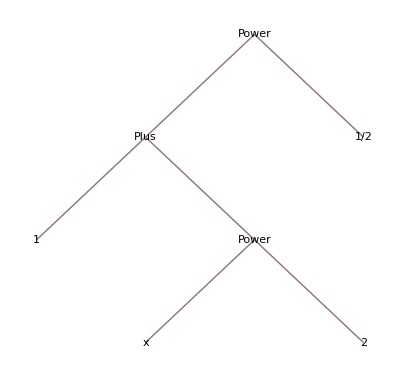

```mathematica
TreeForm[√(1+x^2)]
```

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

Для вызова справки выделить имя и нажать F1
Part[] - ⟦⟧      (* ⟦ ← [[ , ⟧ ← ]] *)
Range[]
Table[]
Subdivide[]

# Правила преобразования

```mathematica
2+2
```

4

```mathematica
2+x
```

2+x

Задание правил

```mathematica
x=4;
```

```mathematica
?x
```

Global`x

x=4

```mathematica
2+x
```

6

Удаление всех правил, ассоциированных с символом

```mathematica
Clear[x]
```

```mathematica
?x
```

Global`x

Set[]  (=)
SetDelayed[]  (:=)

Простое задание правила через = не подходит для определения функций, поскольку вычисляет правую часть до создания правила

```mathematica
x=2;
F[x_]=x^2;
F[3]
```

4

правило с отложенным вычислением

```mathematica
F[x_]:=x^2;
F[3]
```

9

```mathematica
F[0]:=5;
F[x_]:=x^2;
F[x_,_]:=x^3;
```

```mathematica
?F
```

Global`F

F[0]:=5
 
F[x_]:=x^2
 
F[x_,_]:=x^3
 
F[x_,y_,z_]:=z+y^2+F[]

```mathematica
F[0]
```

5

```mathematica
F[3]
```

9

```mathematica
F["kjhsdgfkjh"]
```

kjhsdgfkjh^2

```mathematica
F[0]:=0;
F[1]:=1;
F[n_]:=F[n-1]+F[n-2];  (*определение с использованием рекурсии*)
{F[0],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],F[9]}
```

{0,1,1,2,3,5,8,13,21,34}

```mathematica
"Patterns"paclet:tutorial/PatternsOverview
```

"Specifying Types"paclet:tutorial/SpecifyingTypesOfExpressionInPatterns (F[x_type]:=…)
Optional (F[x_:x0]:=…)
PatternTest (F[x_?test]:=…)
Condition (F[x_/;test]:=…)

Применение функции к списку аргументов = замена заголовка List именем функции:

```mathematica
Apply[F,{s,5}]
```

s^3

краткая запись

```mathematica
F@@{s,5}
```

s^3

```mathematica
ArcTan@@(a+b)
```

ArcTan[a,b]

Три эквивалентных способа записи применения функции к одному аргументу

```mathematica
F@(a)
F[a]
(a)//F
```

a^2

a^2

a^2

```mathematica
"(порядок применения операторов при преобразовании к полной форме)"paclet:tutorial/OperatorInputForms
```

Безымянные (анонимные) функции

```mathematica
Function[{x,y,z},z+y^2]
```

Function[{x,y,z},z+y^2]

```mathematica
Function[{x,y,z},z+y^2][4,5,6]
Function[{x,y,z},z+y^2]@@{4,5,6}
```

краткая запись с использованием безымянных аргументов

```mathematica
(#^2)&
(#1^2+#2)&
```

```mathematica
(#^2)&@5
```

25

```mathematica
(#1^2+#2)&@@{5,3}
```

28

```mathematica
(*использование анонимной функции в качестве аргумента другой функции*)
SortBy[{1,2,3,4,5,6},N[Sin[#]]&]
```

{5,4,6,3,1,2}

# Функциональное программирование

Многие функции по умолчанию применяются к спискам поэлементно

```mathematica
Sin[{1,2,3}]
```

{Sin[1],Sin[2],Sin[3]}

За это отвечает атрибут Listable

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

В частности это позволяет складывать числа со списками или использовать общий множитель

```mathematica
1+{1,2,3}
2*{1,2,3}
```

{2,3,4}

{2,4,6}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

Поэлементное применение функций без атрибута Listable (что, в частности, необходимо для анонимных функций)

```mathematica
Map[(#^2)&,{1,2,3}]
```

{1,4,9}

краткая запись

```mathematica
(#^2)&/@{1,2,3}
```

{1,4,9}

```mathematica
"Functional Operations"paclet:tutorial/FunctionalOperationsOverview
```

Map[] (/@)
Nest[]
Fold[]

```mathematica
Nest[1+1/#&,y,7]
```

1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/y))))))

```mathematica
TeXForm[1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/y))))))]
```

\frac{1}{\frac{1}{\frac{1}{\fr
   ac{1}{\frac{1}{\frac{1}{\fr
   ac{1}{y}+1}+1}+1}+1}+1}+1}+
   1

# Бифуркационная диаграмма

Логистическое отображение

```mathematica
Subscript[x, n+1]=k Subscript[x, n] (1-Subscript[x, n])
```

```mathematica
k=3;
k # (1-#)&;
```

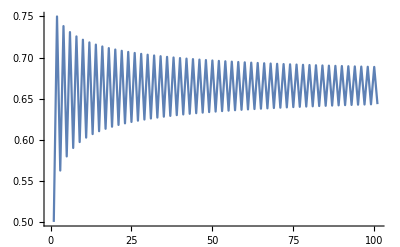

```mathematica
(*динамика системы*)
NestList[k # (1-#)&,0.5,100]//ListLinePlot
```

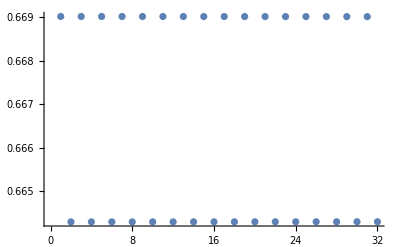

```mathematica
(*предельные точки*)
NestList[k # (1-#)&,0.5,10000]⟦-32;;⟧//ListPlot
```

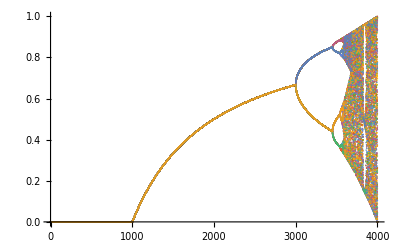

```mathematica
(*полный код для построения бифуркационной диаграммы*)
ListPlot[Table[NestList[k # (1-#)&,0.5,10000]⟦-32;;⟧,{k,0,4,.001}]ᵀ]
```

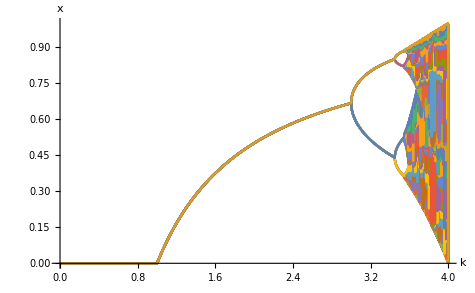

```mathematica
ListLinePlot[Table[Outer[List,{k},Sort[NestList[k #(1-#)&,.5,10000]⟦-32;;⟧]]⟦1⟧,{k,0,4,.001}]ᵀ,AxesLabel->{"k","x"},LabelStyle->Large]
```

# Графики

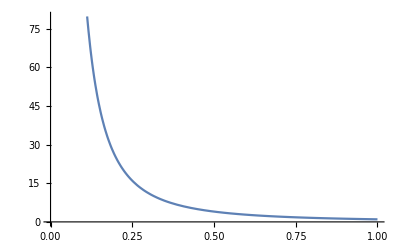

```mathematica
Plot[x^-2,{x,0,1}]
```

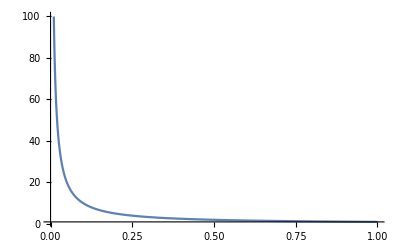

```mathematica
Plot[x^-1,{x,0,1},PlotRange->{{0,1},{1,100}}]
```

Полный список настроек находится в справке функции :

Plot[]
ListPlot[]
ParametricPlot[]
ContourPlot[]
…
Plot3D[]
…

# Подстановки

Для единовременной замены символа без создания глобального правила

```mathematica
Clear[x];
x^2+x/.x-> 5
```

30

```mathematica
?x
```

Global`x

```mathematica
"Transformation Rules and Definitions"paclet:tutorial/TransformationRulesAndDefinitionsOverview
```

ReplaceAll[] (/.)
Rule (→)
RuleDelayed (:>)
ReplaceRepeated[] (//.)

Перед проведением замены все части предварительно вычисляются

```mathematica
y=x;
z=5;
e=x^2+x;

e/.y->z
```

30

:> (вводится как :>)  проводит аналогичную подстановку без предварительного вычисления правой части

```mathematica
{a,a,a}/.a->RandomReal[]
{a,a,a}/.a:>RandomReal[]
```

{0.762553,0.762553,0.762553}

{0.386478,0.221798,0.0285131}

Таблица сравнения вычисляемых частей операторов задания правил и замен

```mathematica
cr=Style["×",Bold,Red,FontSize->54];
ch=Style["✓",Bold,Darker@Green,FontSize->44];
rp=Style["/.",Lighter[Gray,.6]];
chg=Style["✓",Bold,Lighter[Gray,.6],FontSize->44];
Legended[Style[TableForm[{{"","",cr,"=",ch},
{ "","",cr,":=",cr},
{chg,rp,ch,"→",ch},
{chg,rp,ch,":>",cr}},TableSpacing->{1,1},TableHeadings->{None, {"","","","",""}}],FontSize->34],Placed[SwatchLegend[{Darker@Green,Red},{"- evaluated","- unevaluated"},LegendMarkers->{{"✓",25},{"×",40}},LabelStyle->20,LegendLayout->"Row"],Above]]
```

|  |  |  | 
 |  | × | = | ✓
 |  | × | := | ×
✓ | /. | ✓ | → | ✓
✓ | /. | ✓ | :> | ×

Из списка замен к каждому символу применяется не более одного

```mathematica
Clear[x,y,z]
x^2+Sin[y]/.{x->y,y->x}
```

y^2+Sin[x]

При использовании ReplaceRepeated (//.) правила применяются многократно до достижения конечного результата

```mathematica
x^2+Sin[y]//.{x->y,y->z}
```

z^2+Sin[z]

```mathematica
x^2+Sin[y]/.{x->y,y->z}
```

y^2+Sin[z]

# Решение уравнений

Solve[] 
DSolve[] 
NSolve[] 
NDSolve[]

```mathematica
Clear[x]
Solve[x^4+x==0,x]
```

{{x→-1},{x→0},{x→(-1)^(1/3)},{x→-(-1)^(2/3)}}

```mathematica
(*присвоение значения одного из найденных корней исходной переменной*)
x=x/.Solve[x^4+x==0,x]⟦1⟧
```

-1

```mathematica
Clear[x];
sol=NDSolve[{x'[t]==Sin[x[t]^2],x[0]==0.1},{x[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

Использование решения для определения явной функции времени

```mathematica
F=(x[t]/.sol)⟦1,0⟧;
```

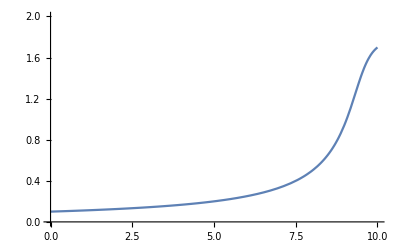

```mathematica
Plot[F[t],{t,0,10},PlotRange->{0,2}]
```

# Центральное поле

```mathematica
Clear[r];
```

```mathematica
F[r_]:=-1/r+1/r^2;
```

```mathematica
sol=NDSolve[{x''[t]==F[r]*x[t]/r,x[0]==0, x'[0]==1, y''[t]==F[r]*y[t]/r,y[0]==1, y'[0]==0}/.{r-> √(x[t]^2+y[t]^2)},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

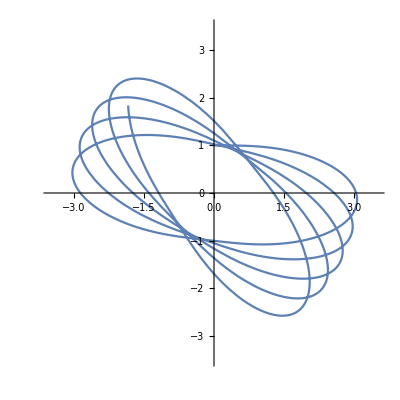

```mathematica
Manipulate[
ParametricPlot[{sol[[1,1,2]],sol[[1,2,2]]},{t,0,T},PlotRange->3.5{{-1,1},{-1,1}}]
,{T,0.1,100}]
```

```mathematica
(*решение аналогичной задачи с использованием векторной переменной*)
F[r_]:=-1/r+(1/3)/r^2;
Clear[rv,t];
T=100;
sol2=NDSolve[{rv''[t]==F[Norm[rv[t]]] rv[t]/Norm[rv[t]],rv[0]=={0,1.5},rv'[0]=={.5,0}},{rv[t]},{t,0,T}]⟦1⟧;
solF=Function[t,Evaluate[rv[t]/.sol2]];
pic[t_]:=Module[{points,r},
lt=5;np=250; (*длинна следа траектории и количество точек для его отрисовки*)
points=solF/@Select[Subdivide[t-lt,t,np],#≥0&]; (*точки следа*)
Graphics[{Thickness[0.005],RGBColor[1, 0.7000000000000001, 0.21],Line[points],Disk[points⟦-1⟧,0.06],RGBColor[0.38, 0.27, 0.8],Disk[{0,0},0.15]},PlotRange->2{{-1,1},{-1,1}},AspectRatio->1,Background->White]
]

Manipulate[pic[tt],{tt,0,T}]
```